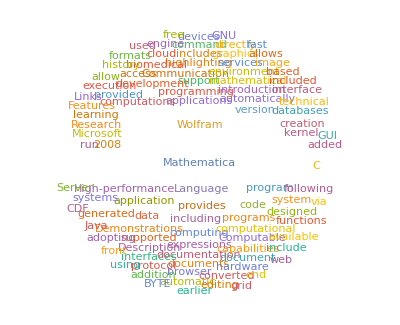

```mathematica
WordCloud[WikipediaData["Mathematica"]]
```

```mathematica
Crash Course in Mathematica for Graduate Students
```

## Introduction Lesson 1

In MATHEMATICA we can solve symbolic expressions

```mathematica
Solve[a x^2+b x+c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

and solve maths problem like ODEs

```mathematica
DSolve[{x''[t]+3 x'[t]+2x[t]==0, 
x[0]==1, x'[0]==0}, x[t], t ]
```

{{x[t]→ⅇ^(-2 t) (-1+2 ⅇ^t)}}

It is possible to assign a particular value to a variable

```mathematica
a = 2; (*and suppress undesired outputs*)
b = 3;
a + b
```

5

It is possible to compute integrals

```mathematica
Integrate[Sin[x]/x, {x, -Infinity, Infinity}]
```

π

also in a eye-candy way [2]

```mathematica
∫_(-∞)^(+∞) Sin[x]/x ⅆx
```

π

It is easy to make simple plots

```mathematica
func = A Sin[ω t + ϕ];
parameters = {A-> 2, ω->0.3, ϕ-> 0.1};
ReplaceAll[func, parameters] (*a lot of handy shortcuts exist!*)
```

2 Sin[0.1+0.3 t]

```mathematica
func /. parameters
```

2 Sin[0.1+0.3 t]

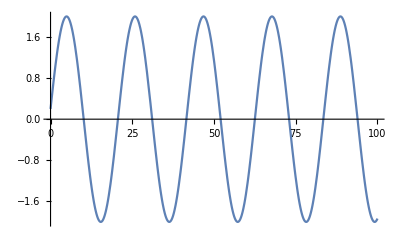

```mathematica
Plot[%, {t, 0, 100}]
```

Obviously you must specifies numerical values for all the parameters, or you can manipulate them...

```mathematica
Manipulate[Plot[A Sin[ω t + ϕ], {t, 0, 100}],{ A, 2, 10}, {ω, 0.3, 1}, {ϕ, 0.1, 10}]
```

You can also manipulate different objects

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}]
```

The idea now is to solve some simple (if you have a bachelor degree in physics) physical problems using MATHEMATICA. Doing this we will discover the main feature of this language.
All the exercise in this lessons are taken from [1]. A more exhaustive treatment can be found in this book. A suggested reading.

## Moving object with non-trivial EoM

Consider an object with the following EoM

Find velocity and acceleration. Plots these along with the position on a single graph with legends. Find the time(s) at which there is no net force on the object.

```mathematica
position[t_]=5t Exp[-t^2]
velocity[t_]= D[position[t], t]
acceleration[t_]=D[velocity[t], t]
```

5 ⅇ^(-t^2) t

5 ⅇ^(-t^2)-10 ⅇ^(-t^2) t^2

-30 ⅇ^(-t^2) t+20 ⅇ^(-t^2) t^3

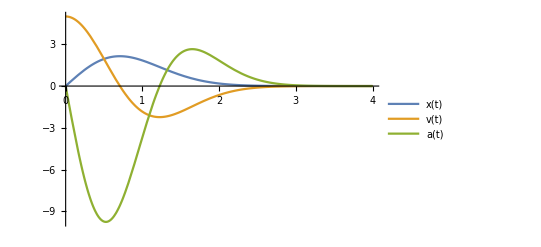

```mathematica
Plot[{position[t], velocity[t], acceleration[t]}, {t, 0,4 }, PlotLegends->{"x(t)", "v(t)", "a(t)"}, PlotRange->Full]
```

```mathematica
Solve[acceleration[t]==0, t, Assumptions->{t≥0}]
```

{{t→0},{t→√(3/2)}}

```mathematica
Limit[acceleration[t], t->∞]
```

0

## Gravity near the Earth’s surface

Find an expression up to second order for the modification to g for an object at the height h. We need to find a small parameter to expand in series on it.

```mathematica
force = G m M / (R+h)^2;
Series[force/.h-> x R, {x, 0, 2}];
forcex = Normal[%]/.x-> h/R
```

(3 G h^2 m M)/R^4-(2 G h m M)/R^3+(G m M)/R^2

Now we can express G in term of the usual gravity acceleration g.

```mathematica
grepl = Solve[g==G M / R^2, G];
forcex/.grepl
```

{g m+(3 g h^2 m)/R^2-(2 g h m)/R}

## Pendulum period

Consider a very standard pendulum: string of length l with a blob of mass m in the end. We know the period is 2π √(l/g) but this is accurate only if the maximum displacement satisfies θ_0<<1 . How to find an expression for the period as a function of θ_0?

From energy conservation we have that energy at θ = θ_0 is equal to the energy at θ = 0.  Thus

We can reduce this equation to an expression for the angular velocity .

(We choose the minus sign because we’ll be thinking about the quarter period of the pendulum if it is released from rest at , hence the angle is decreasing.
The period is four times the time it takes to go from  to .

This is a scary integral and there is no closed analytic form for it, but it is no problem for MATHEMATICA.

```mathematica
int = Integrate[1/(√(Cos[θ]- Cos[θ0])), {θ, θ0, 0}, Assumptions->{θ0>0 && θ0< Pi}]
```

-(2 EllipticF[θ0/2,Csc[θ0/2]^2])/(√(1-Cos[θ0]))

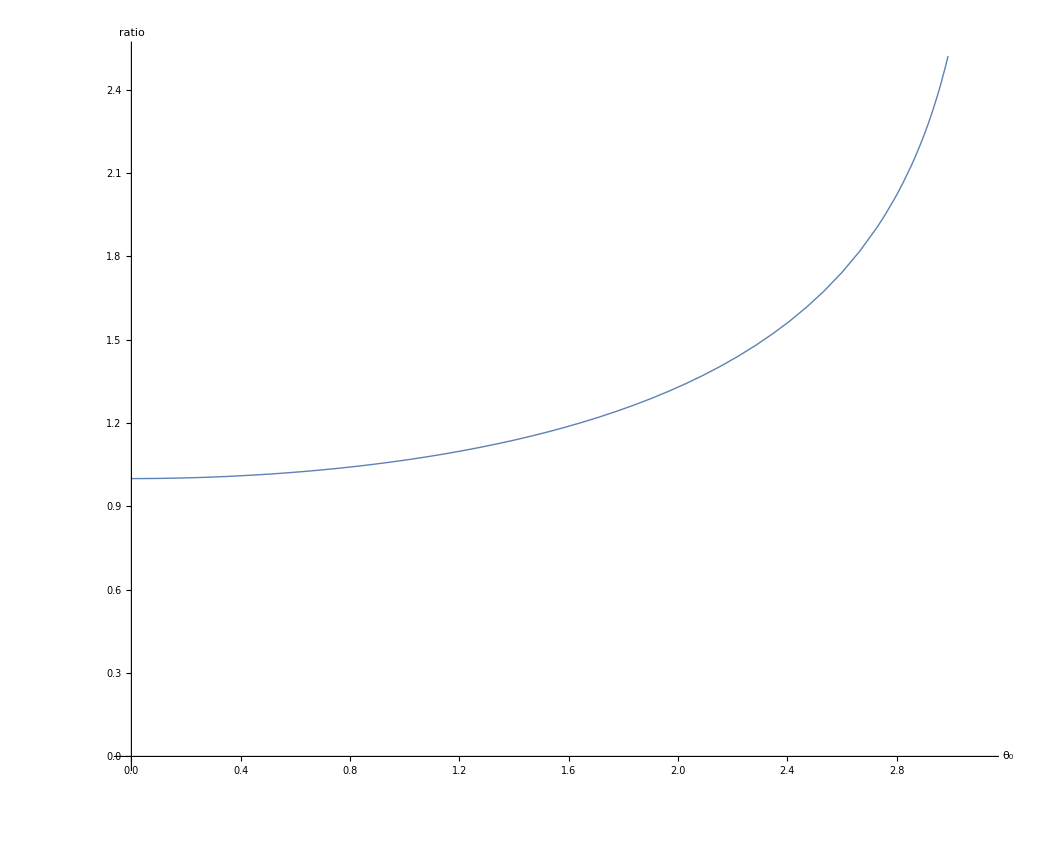

```mathematica
period = -4 √(l/(2g))int;
ratio = period / (2π √(l/g));
Plot[ratio, {θ0, 0, 0.99Pi},PlotStyle->Thick, AspectRatio->Full, AxesLabel->{Subscript[θ, 0], "ratio"}, AxesOrigin->{0, 0}]
```

## A Falling Ball with Drag

Consider a mass , initially at rest, dropped from a height  and subject to a linear drag force  proportional to the velocity.
Find an expression for its height as a function of time and plot it for various value of .

We need to solve the following differential equation

```mathematica
Clear[m, g]
Clear[b]
```

```mathematica
DSolve[{m y''[t]==-m g-b y'[t], y[0]==h, y'[0]==0} , y, t];
height=Simplify@First[y[t]/.%]
```

h+(g m (m-ⅇ^(-(b t)/m) m-b t))/b^2

Check the limit

```mathematica
Limit[height, b->0]
```

h-(g t^2)/2

```mathematica
mgh={m->0.1, g->9.8, h->100};
m1=Manipulate[
Plot[height/.mgh/.b->drag, {t, 0, 15},
PlotRange->{0, 100}, 
AxesLabel->{"t", "h(t)"}],
{drag, 0.0001, 1}]
```

Instead the velocity is

```mathematica
velocity=D[height, t]
```

((-b+b ⅇ^(-(b t)/m)) g m)/b^2

```mathematica
Limit[velocity, t->∞]
```

ConditionalExpression[-(g m)/b, g∈ℝ&&b m>0]

```mathematica
Plot[Evaluate@Table[velocity/.mgh, {b, {0.001,0.005, 0.01,0.05, 0.1 }}], {t, 0, 100},PlotLabels->{0.001,0.005, 0.01,0.05, 0.1 }] (*here I used labels instead of legends*)
```

-Graphics-

## Fourier Series

Consider the function . Obtain and plot the Fourier series of this function. 
Since it is an odd function only the sine components should be different from zero.

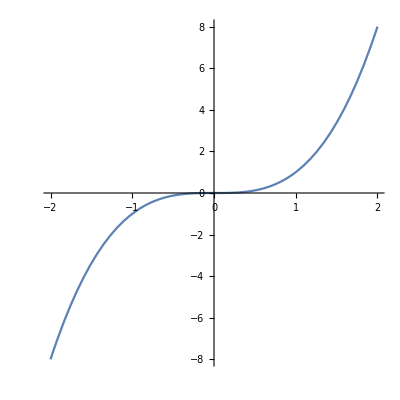

```mathematica
f[x_]=x^3;
Plot[f[x], {x, -2, 2}, AspectRatio->1]
```

```mathematica
a[n_]=1/Pi Integrate[f[x]*Cos[n*x], {x, -Pi, Pi}]
b[n_]=1/Pi Integrate[f[x]*Sin[n*x], {x, -Pi, Pi}]
```

Set::write: Tag Integer in 2[n_] is Protected.

0

(-2 n π (-6+n^2 π^2) Cos[n π]+6 (-2+n^2 π^2) Sin[n π])/(n^4 π)

```mathematica
Table[b[n], {n ,1, 10}] (*the first 10 coefficients*)
```

{2 (-6+π^2),1/4 (6-4 π^2),2/27 (-6+9 π^2),1/32 (6-16 π^2),2/125 (-6+25 π^2),1/108 (6-36 π^2),2/343 (-6+49 π^2),1/256 (6-64 π^2),2/729 (-6+81 π^2),1/500 (6-100 π^2)}

It is easy to obtain the series now and do a comparison

```mathematica
F[x_, Nmax_]:=Sum[b[n]*Sin[n x], {n, 1, Nmax}]  (*:= instead of = maintain the rhs in a unevaluated form*)
Manipulate[Plot[{f[x], F[x, Nmax]}, {x, -Pi, Pi}], {Nmax, 2, 20}]
```

## Introduction Lesson 2

In the previous lesson we played with calculus but MATHEMATICA is good also for doing linear algebra calculations which are common in physics.
We can define vector of elements simply doing

```mathematica
v= {1, 3, 5}
w = {2, 4, 6}
v+w
```

{1,3,5}

{2,4,6}

{3,7,11}

And also matrices

```mathematica
M = {{1, 3, 5}, {2, 5, 8}, {1, 4, 9}}//MatrixForm (*gives the Matrix-like output*)
```

(1 | 3 | 5
2 | 5 | 8
1 | 4 | 9)

Obviously all the standard operation between vector and matrices are allowed,  but only in the ‘original version’.

```mathematica
v={1, 2, 3}//MatrixForm
M.v
```

(1
2
3)

(1 | 3 | 5
2 | 5 | 8
1 | 4 | 9).(1
2
3)

```mathematica
M = {{1, 3, 5}, {2, 5, 8}, {1, 4, 9}};
v={1, 2, 3}
M.v
M.v//MatrixForm
```

{1,2,3}

{22,36,36}

(22
36
36)

Matrices and vectors are lists for MATHEMATICA. We have access to their elements simply

```mathematica
M[[1]] (*first row*)
```

{1,3,5}

```mathematica
M[[1, 3]](*first row but also third column*)
M[[1]][[ 3]](*but the meaning of this is slightly different*)
```

5

5

```mathematica
M[[All , 3]](*only the third column*)
```

{5,8,9}

Lists are more general object. For more info see [4].

## Current in DC Circuit

Consider the DC circuit in the picture above. Use Kirchoff’s Laws to determine the currents i_1, i_2 and i_3 in terms of V, R_1, R_2 and R_3.
Kirchoff’s node and loops lwas give us the following equations:

We can define the equations

```mathematica
eq1 = i1 == i2 + i3;
eq2 = V == i1 R1 + i2 R2;
eq3 = 0 == i2 R2 - i3 R3;
eq4 = V == i1 R1 + i3 R3;
```

And solve them

```mathematica
Solve[{eq1, eq2, eq3}, {i1, i2, i3}]
```

{{i1→((R2+R3) V)/(R1 R2+R1 R3+R2 R3),i2→(R3 V)/(R1 R2+R1 R3+R2 R3),i3→(R2 V)/(R1 R2+R1 R3+R2 R3)}}

They correspond to this matrix.

```mathematica
M={{-1, 1, 1},{R1, R2, 0},{0, R2, -R3}}//Transpose;
{{-1, 1, 1},{R1, R2, 0},{0, R2, -R3}}//Transpose//MatrixForm
```

(-1 | R1 | 0
1 | R2 | R2
1 | 0 | -R3)

with these homogeneous part

```mathematica
v={0, V, 0};
{0, V, 0}//MatrixForm
```

(0
V
0)

```mathematica
LinearSolve[M, v]
```

{(R1 R3 V)/(R1 R2+R1 R3+R2 R3),(R3 V)/(R1 R2+R1 R3+R2 R3),(R1 V)/(R1 R2+R1 R3+R2 R3)}

## Special Relativity and Boosted Objects

If we define the Lorentzian metric as the matrix

```mathematica
g=DiagonalMatrix[{1, -1, -1, -1}];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

we can use it to compute scalar product in Minkowski space.

```mathematica
v1= {1, 0, 0, 1};
v2={1, 0, 0, -1};
v2.g.v1 (*this is the same than the Dot[] function*)
```

2

Consider a pion ( π ) at rest which decays into two photons ( γ ).  In the rest frame of the pion the μ and the ν will decay in a back-to-back configuration.

Thus the 4-vectors are

```mathematica
Subscript[p, π]={m0, 0, 0, 0};  (*Rest frame 4-vectors*)
p1={ω, 0, 0, ω};
p2={ω, 0, 0, -ω};
```

```mathematica
a=Part[p1,2;;4];
b=Part[p2, 2;;4];
ma=Sqrt[Transpose[a].a];
mb=Sqrt[Transpose[b].b];
Solve[Transpose@a.b == Cos[α] ma mb, Cos[α]]
```

{{Cos[α]→-1}}

Compute how the angle between the two photons varies in a generic boosted frame in the x directions. Plot θ(β).

```mathematica
γ=1/(√(1-β^2));
Λ={{γ, -γ β, 0, 0},{-γ β,γ, 0, 0},{0, 0, 1, 0},{0, 0, 0, 1}}; (*Lorenz transformation*)
{{γ, -γ β, 0, 0},{-γ β,γ, 0, 0},{0, 0, 1, 0},{0, 0, 0, 1}}//MatrixForm
```

(1/(√(1-β^2)) | -β/(√(1-β^2)) | 0 | 0
-β/(√(1-β^2)) | 1/(√(1-β^2)) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Subscript[pulse, π]=Part[Λ.Subscript[p, π], 2;;4] (*the same than the [[]] command*)
pulse1=Part[Λ.p1, 2;;4]
pulse2=Part[Λ.p2, 2;;4]
```

{-(m0 β)/(√(1-β^2)),0,0}

{-(β ω)/(√(1-β^2)),0,ω}

{-(β ω)/(√(1-β^2)),0,-ω}

```mathematica
mod1=Sqrt[Transpose[pulse1].pulse1];
mod2=Sqrt[Transpose[pulse2].pulse2];
mod1 mod2 Cos[θ]==Transpose[pulse1].pulse2 /.ω->m0/2
Simplify@Solve[%,Cos[θ]]
```

(m0^2/4+(m0^2 β^2)/(4 (1-β^2))) Cos[θ]==-m0^2/4+(m0^2 β^2)/(4 (1-β^2))

{{Cos[θ]→-1+2 β^2}}

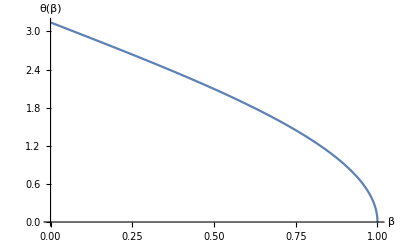

```mathematica
Plot[ArcCos[-1+2 β^2], {β, 0, 1}, AxesLabel->{β, "θ(β)"}]
```

## Inertia Tensor and Principal Axes

The most general notion of moment of inertia is encoded in the inertia tensor.

Measured in the body frame  is a constant real symmetric matrix, hence it admits a decomposition into a rotation matrix  and a diagonal matrix  such that

Columns of the rotation matrix  define the directions of the principal axes of the body. If  the scalar  and  are called principal moments of inertia.
Given the mass distribution below compute the inertia tensor for this body and find its principal axes/moments.

```mathematica
Ω=Cylinder[{{0,0,0},{1,1,1}},1/2]; (*A cylinder from the origin to {1,1,1} with radius 1/2:*)
Graphics3D[Ω]
```

-Graphics3D-

```mathematica
V=Integrate[1, Element[X, Ω]] (*Volume of the ellipsoid*)
cm=1/V Integrate[X, Element[X, Ω]] (*center of mass*)
```

(√3 π)/4

{1/2,1/2,1/2}

```mathematica
(*between X and {r, θ, z} there are intermidiate coordinates X'=RX*)
```

```mathematica
R=RotationMatrix[{{0, 0, 1}, {1, 1, 1}}]; (*rotates the first vector in the second one*)
%//MatrixForm
```

(1/6 (3+√3) | 1/6 (-3+√3) | 1/(√3)
1/6 (-3+√3) | 1/6 (3+√3) | 1/(√3)
-1/(√3) | -1/(√3) | 1/(√3))

```mathematica
X={x, y, z};
X2=R.X-cm;
m=Dot[X2,X2]IdentityMatrix[3]-Outer[Times, X2, X2]/.{x->r Cos[θ], y->r Sin[θ]}//FullSimplify;
%//MatrixForm (*inertia tensor in cylindrical coordinates*)
```

(1/36 ((-3+2 √3 z+(-3+√3) r Cos[θ]+(3+√3) r Sin[θ])^2+(3-2 √3 z+2 √3 r (Cos[θ]+Sin[θ]))^2) | 1/12 (-3+4 √3 z-4 z^2+2 r (√3-2 z) (Cos[θ]+Sin[θ])+2 r^2 (1-4 Cos[θ] Sin[θ])) | -1/36 (-3+2 √3 z+(3+√3) r Cos[θ]+(-3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ]))
1/12 (-3+4 √3 z-4 z^2+2 r (√3-2 z) (Cos[θ]+Sin[θ])+2 r^2 (1-4 Cos[θ] Sin[θ])) | 1/36 ((-3+2 √3 z+(3+√3) r Cos[θ]+(-3+√3) r Sin[θ])^2+(3-2 √3 z+2 √3 r (Cos[θ]+Sin[θ]))^2) | -1/36 (-3+2 √3 z+(-3+√3) r Cos[θ]+(3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ]))
-1/36 (-3+2 √3 z+(3+√3) r Cos[θ]+(-3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ])) | -1/36 (-3+2 √3 z+(-3+√3) r Cos[θ]+(3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ])) | 1/6 (3-4 √3 z+4 z^2-2 r (√3-2 z) (Cos[θ]+Sin[θ])-2 r^2 (-2+Sin[2 θ])))

```mathematica
Inertia=MomentOfInertia[Ω]; (*compute it for our rotated cylinder it would not have been easy*)
%//MatrixForm  (*if not specified it computes the inertia tensor wrt the cm*)
```

((√3 π)/16 | -(√3 π)/64 | -(√3 π)/64
-(√3 π)/64 | (√3 π)/16 | -(√3 π)/64
-(√3 π)/64 | -(√3 π)/64 | (√3 π)/16)

```mathematica
P=Transpose@Eigenvectors[Inertia];
%//MatrixForm
Eigenvalues[Inertia]
```

(-1 | -1 | 1
0 | 1 | 1
1 | 0 | 1)

{(5 √3 π)/64,(5 √3 π)/64,(√3 π)/32}

Let me check they are eigenvectors

```mathematica
Table[v=P[[All, i]];
Solve[Inertia.v== λ v, λ], {i, 1, 3}]
```

{{{λ→(5 √3 π)/64}},{{λ→(5 √3 π)/64}},{{λ→(√3 π)/32}}}

```mathematica
Inverse[P].Inertia.P//FullSimplify;
%//MatrixForm (*which is diagonal*)
```

((5 √3 π)/64 | 0 | 0
0 | (5 √3 π)/64 | 0
0 | 0 | (√3 π)/32)

Adding the jacobian we can also use the inertia tensor definition to obtain the same result.

```mathematica
Inertia2=Integrate[m*r, {r, 0, 1/2},{θ, -Pi, Pi},{z, 0, Sqrt[3]}];(*they are the same!*)
%//MatrixForm
```

((√3 π)/16 | -(√3 π)/64 | -(√3 π)/64
-(√3 π)/64 | (√3 π)/16 | -(√3 π)/64
-(√3 π)/64 | -(√3 π)/64 | (√3 π)/16)

## Eigenmodes of the Heat Equation

The Heat Equation is

Using the DEigensystem function we can easily find heat equation smallest eigenfunctions and eigenvalues.

```mathematica
Nmax=20;
{ℒ,ℬ}={D[u[t,x],t]==Laplacian[u[t,x],{x}],DirichletCondition[u[t,x]==0,True]};
{vals,funs}=DEigensystem[{ℒ,ℬ},u[t,x],t,{x,0,1},Nmax]
```

{{-π^2,-4 π^2,-9 π^2,-16 π^2,-25 π^2,-36 π^2,-49 π^2,-64 π^2,-81 π^2,-100 π^2,-121 π^2,-144 π^2,-169 π^2,-196 π^2,-225 π^2,-256 π^2,-289 π^2,-324 π^2,-361 π^2,-400 π^2},{ⅇ^(-π^2 t) Sin[π x],ⅇ^(-4 π^2 t) Sin[2 π x],ⅇ^(-9 π^2 t) Sin[3 π x],ⅇ^(-16 π^2 t) Sin[4 π x],ⅇ^(-25 π^2 t) Sin[5 π x],ⅇ^(-36 π^2 t) Sin[6 π x],ⅇ^(-49 π^2 t) Sin[7 π x],ⅇ^(-64 π^2 t) Sin[8 π x],ⅇ^(-81 π^2 t) Sin[9 π x],ⅇ^(-100 π^2 t) Sin[10 π x],ⅇ^(-121 π^2 t) Sin[11 π x],ⅇ^(-144 π^2 t) Sin[12 π x],ⅇ^(-169 π^2 t) Sin[13 π x],ⅇ^(-196 π^2 t) Sin[14 π x],ⅇ^(-225 π^2 t) Sin[15 π x],ⅇ^(-256 π^2 t) Sin[16 π x],ⅇ^(-289 π^2 t) Sin[17 π x],ⅇ^(-324 π^2 t) Sin[18 π x],ⅇ^(-361 π^2 t) Sin[19 π x],ⅇ^(-400 π^2 t) Sin[20 π x]}}

We can plot them and notice that they are damped from the time exponential.

```mathematica
Table[Plot3D[funs[[i]],{x,-1,1},{t,0,0.2},PlotRange->All,Ticks->False,Mesh->False],{i,Nmax}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*It is possible to decompose an arbitrary function on the eigenfunction base and study the evolution of the system with this as an initial condition?*)
```

```mathematica
Code Here
```

```mathematica
L2norm[f1_, f2_, Domain_:{x, 0, 1}]:=Module[{},
Integrate[Conjugate[f2]*f1, Domain]
]
```

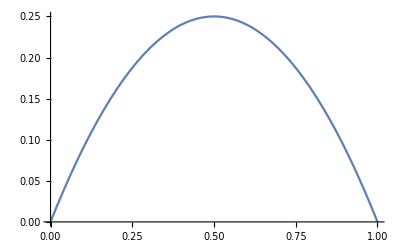

```mathematica
f[x_]=x(1-x); (*our function*)
Plot[%, {x, 0, 1}]
```

```mathematica
coeff[t_]=Table[L2norm[f[x], funs[[i]]], {i, 1, Nmax}] (*the coefficient on the eigenfunction bases*)
```

{(4 ⅇ^(-π^2 Conjugate[t]))/π^3,0,(4 ⅇ^(-9 π^2 Conjugate[t]))/(27 π^3),0,(4 ⅇ^(-25 π^2 Conjugate[t]))/(125 π^3),0,(4 ⅇ^(-49 π^2 Conjugate[t]))/(343 π^3),0,(4 ⅇ^(-81 π^2 Conjugate[t]))/(729 π^3),0,(4 ⅇ^(-121 π^2 Conjugate[t]))/(1331 π^3),0,(4 ⅇ^(-169 π^2 Conjugate[t]))/(2197 π^3),0,(4 ⅇ^(-225 π^2 Conjugate[t]))/(3375 π^3),0,(4 ⅇ^(-289 π^2 Conjugate[t]))/(4913 π^3),0,(4 ⅇ^(-361 π^2 Conjugate[t]))/(6859 π^3),0}

```mathematica
expr[t_, x_]=Sum[coeff[0][[i]]*funs[[i]], {i, 1, Nmax}] (*the expansion*)
```

(4 ⅇ^(-π^2 t) Sin[π x])/π^3+(4 ⅇ^(-9 π^2 t) Sin[3 π x])/(27 π^3)+(4 ⅇ^(-25 π^2 t) Sin[5 π x])/(125 π^3)+(4 ⅇ^(-49 π^2 t) Sin[7 π x])/(343 π^3)+(4 ⅇ^(-81 π^2 t) Sin[9 π x])/(729 π^3)+(4 ⅇ^(-121 π^2 t) Sin[11 π x])/(1331 π^3)+(4 ⅇ^(-169 π^2 t) Sin[13 π x])/(2197 π^3)+(4 ⅇ^(-225 π^2 t) Sin[15 π x])/(3375 π^3)+(4 ⅇ^(-289 π^2 t) Sin[17 π x])/(4913 π^3)+(4 ⅇ^(-361 π^2 t) Sin[19 π x])/(6859 π^3)

```mathematica
Plot3D[expr[t, x], {x, 0, 1}, {t, 0, 0.5}, PlotRange->All, Mesh->False, Ticks->False]
```

-Graphics3D-

## Introduction Lesson 3

In the previous lessons we learnt a lot about the main functionalities of MATHEMATICA, but there is a lot of more! For example we can do other funny stuff using 3D plots.

```mathematica
expr[l_, m_]:=FullSimplify@Abs[SphericalHarmonicY[l,m,θ,ϕ]]^2;
Table[Table[{StringForm["l= ``",l], StringForm["m=± ``",m], expr[l, m],SphericalPlot3D[{Abs[SphericalHarmonicY[l,m,θ,ϕ]^2]},{θ,0,Pi},{ϕ,0,2 Pi}, PlotRange->All, Boxed->False, Axes->False]},{m,0,l}], {l, 0,3}]//TableForm
```

l= 0
m=± 0
1/(4 π)
-Graphics3D- |  |  | 
l= 1
m=± 0
(3 Abs[Cos[θ]]^2)/(4 π)
-Graphics3D- | l= 1
m=± 1
(3 ⅇ^(-2 Im[ϕ]) Abs[Sin[θ]]^2)/(8 π)
-Graphics3D- |  | 
l= 2
m=± 0
(5 Abs[1-3 Cos[θ]^2]^2)/(16 π)
-Graphics3D- | l= 2
m=± 1
(15 ⅇ^(-2 Im[ϕ]) Abs[Sin[2 θ]]^2)/(32 π)
-Graphics3D- | l= 2
m=± 2
(15 ⅇ^(-4 Im[ϕ]) Abs[Sin[θ]]^4)/(32 π)
-Graphics3D- | 
l= 3
m=± 0
(7 Abs[3 Cos[θ]-5 Cos[θ]^3]^2)/(16 π)
-Graphics3D- | l= 3
m=± 1
(21 ⅇ^(-2 Im[ϕ]) Abs[Sin[θ]-5 Cos[θ]^2 Sin[θ]]^2)/(64 π)
-Graphics3D- | l= 3
m=± 2
(105 ⅇ^(-4 Im[ϕ]) Abs[Cos[θ] Sin[θ]^2]^2)/(32 π)
-Graphics3D- | l= 3
m=± 3
(35 ⅇ^(-6 Im[ϕ]) Abs[Sin[θ]]^6)/(64 π)
-Graphics3D-

The plots above should be familiar to you... They are Spherical Harmonics! The same you have encountered in the hydrogen atom in QM.
But also different kind of computation than the ‘traditional calculus problems’ are possible. For example this is a so-called cellular automaton

```mathematica
RulePlot[CellularAutomaton[30], {{1}, 0}, 50, Mesh->True, PlotLegends->"Icon", ImageSize->Large]
```

-Graphics-

This simple model can describe heat diffusion very well!
Now let me give you an outlook on some advanced functionalities of MATHEMATICA ...

## Fun with Random Numbers

Do you know how Monte Carlo methods work? Monte Carlo are a broad class of computational algorithms that rely on repeated random sampling to obtain numerical results.  
If you are not confident with MCs take a look at this simple but inspiring example: this is how I figured out MCs.

Consider a  square and a quarter of the radius 1 circle built with the origin on one of the corner of the square. Now spread in the plane a lot of points randomly. The probability that a single point is inside the circle-quarter is proportional to the ratio between its area and the (total) square area.

P_(d e i^2 n s)≈π/4

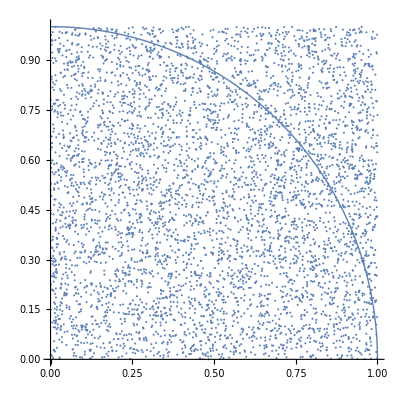

```mathematica
nGen = 5 10^3;
points = RandomReal[{0, 1}, {nGen, 2}];
Show[
ListPlot[points, 
PlotRange->{{0, 1}, {0, 1}}],
Plot[Sqrt[1-x^2], {x, 0, 1}, 
PlotStyle->Thick],
AspectRatio->1]
```

It is easy for us to compute this probability using the frequentist interpretation of probability. Hence we are able to estimate the π.

```mathematica
points[[1]]
(points[[1]])[[1]]
```

{0.922074,0.693543}

0.922074

```mathematica
nPi=Length[Select[points,Sqrt[#[[1]]^2+#[[2]]^2]<1&]]
nPi=Length[Select[points, Dot[#, #]<1&]]
```

3919

3919

```mathematica
N[4*nPi/nGen]
```

3.1352

## Fun with Databases

We can do the same we have done for the cylinder but using weird object in the database.

```mathematica
wrench=ExampleData[{"Geometry3D","Wrench"},"Region"]
```

-Graphics3D-

```mathematica
point={-8,-0.168,0};
Show[wrench,Graphics3D[{PointSize[Large],Point[point]}],ViewPoint->{0,-∞,0}]
```

-Graphics3D-

```mathematica
Inertia=MomentOfInertia[wrench,point]
principalaxes=Eigenvectors[Inertia]
inertiaellipsoid=Ellipsoid[point,1000 Inverse[Inertia]]
```

{{229.671,4.12838,36.4835},{4.12838,23219.4,-0.160962},{36.4835,-0.160962,23004.6}}

{{0.000178434,1.,-0.000718987},{0.00160204,0.000718701,0.999998},{0.999999,-0.000179586,-0.00160191}}

Ellipsoid[{-8,-0.168,0},{{4.35517,-0.000774391,-0.00690696},{-0.000774391,0.0430675,1.52947×10^-6},{-0.00690696,1.52947×10^-6,0.0434805}}]

```mathematica
axes=Graphics3D[{Opacity[1],Arrowheads[{-0.04,0.04}],{Specularity[Gray,10],Gray,inertiaellipsoid},MapThread[{RGBColor[#2],Arrow[Tube[{point-4 #,point+4 #},.06]]}&,{principalaxes,IdentityMatrix[3]}]}];
Show[wrench,axes,BaseStyle->Opacity[0.3]]
```

-Graphics3D-

Also countries data are available.

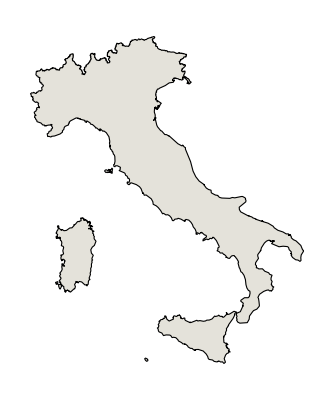

```mathematica
CountryData["Italy", "Shape"]
```

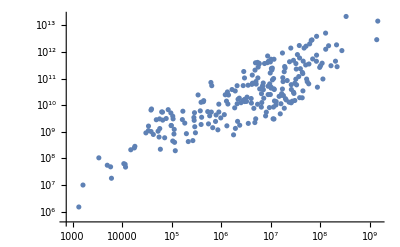

```mathematica
ListLogLogPlot[
 Tooltip[{CountryData[#, "Population"], CountryData[#, "GDP"]}, 
    CountryData[#, "Name"]] & /@ CountryData["Countries"]]
```

Oss.: Also the WordCloud I used as head image...

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
Length[titanic]
```

1309

```mathematica
RandomSample[titanic,5]
Normal[%]
```

{<|class→3rd,age→24,sex→male,survived→False|>,<|class→1st,age→55,sex→female,survived→True|>,<|class→3rd,age→Missing[],sex→male,survived→False|>,<|class→3rd,age→21,sex→female,survived→False|>,<|class→2nd,age→26,sex→male,survived→False|>}

```mathematica
titanic[Count[_Missing],"age"]
```

263

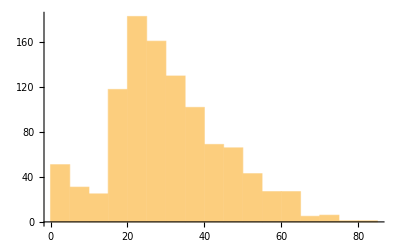

```mathematica
titanic[Histogram,"age"]
```

```mathematica
titanic[Max,"age"]
```

80

```mathematica
ratio[list_]:=list//Boole//Mean//N;
titanic[GroupBy["sex"],GroupBy["class"],ratio,"survived"]
```

## Fun with Animations

The code here is taken from [5]. In general looking inside the Wolfram Community is always a good idea if you want to find interesting stuff.

```mathematica
ClearAll (*clear variables saves life*)
```

ClearAll

```mathematica
terms=20;
λx[1]=N[Table[n π,{n,1,terms}]];
λy[1]=N[Table[(m π)/A,{m,1,terms}]];
λ2[1]=Table[(λx[1][[m]])^2+(λy[1][[n]])^2,{m,1,terms},{n,1,terms}];
λx[2]=N[Table[n π,{n,0,terms-1}]];
λy[2]=N[Table[(m π)/A,{m,0,terms-1}]];
λ2[2]=Table[(λx[2][[m]])^2+(λy[2][[n]])^2,{m,1,terms},{n,1,terms}];
ψx[1]=Sin[λx[1]*x];
ψy[1]=Sin[λy[1]*y];
ψ[1]=Transpose[{ψx[1]}].{ψy[1]};
ψx[2]=Cos[λx[2]*x];
ψy[2]=Cos[λy[2]*y];
ψ[2]=Transpose[{ψx[2]}].{ψy[2]};
Nx[1]=Table[1/2,{i,1,terms}];
Ny[1]=Table[A/2,{i,1,terms}];
Nx[2]=Prepend[Table[1/2,{i,1,terms-1}],1];
Ny[2]=Prepend[Table[A/2,{i,1,terms-1}],A];
ψxint[1]=1/Nx[1](Integrate[Sin[lam*x],{x,xstart,xend}]/.lam->λx[1]);
ψyint[1]=1/Ny[1](Integrate[Sin[lam*y],{y,ystart,yend}]/.lam->λy[1]);
ψint[1]=Transpose[{ψxint[1]}].{ψyint[1]};
ψxint[2]=1/Nx[2] Prepend[Integrate[Cos[lam*x],{x,xstart,xend}]/.lam->λx[2][[2;;terms]],(xend-xstart)];
ψyint[2]=1/Ny[2] Prepend[Integrate[Cos[lam*y],{y,ystart,yend}]/.lam->λy[2][[2;;terms]],(yend-ystart)];
ψint[2]=Transpose[{ψxint[2]}].{ψyint[2]};
Eint[1]=2*Exp[-B*t/2]*Sin[t/2*√(4*λ2[1]-B^2)]/√(4*λ2[1]-B^2);
Eint[2]=2*Exp[-B*t/2]*Sin[t/2*√(4*λ2[2]-B^2)]/√(4*λ2[2]-B^2);
Solution[1][x_,y_,t_,xstart_,ystart_,xend_,yend_,A_,B_]=Total[Eint[1]*ψint[1]*ψ[1],2];
Solution[2][x_,y_,t_,xstart_,ystart_,xend_,yend_,A_,B_]=Total[Eint[2]*ψint[2]*ψ[2],2];
```

```mathematica
Manipulate[
If[Spts[[2]]>A-.05,Spts={Spts[[1]],A-.05}];
Plot3D[
Evaluate[
Solution[BC][x,y,t,Spts[[1]]-.05,Spts[[2]]-.05,Spts[[1]]+.05,Spts[[2]]+.05,A,B]
],
{x,0,1},{y,0,A},
PlotRange->0.04{-1,1},
BoxRatios->{1,A,5/8},
PlotPoints->ControlActive[30,50],
MaxRecursion->2,
Boxed->False,
Axes->False,
Mesh-> False,
SphericalRegion-> True],
{{t,0,"time"},0,2*√2,0.01,Appearance->"Labeled"},
{{A,1,"aspect ratio"},.1,1,Appearance->"Labeled"},
{{B,0.001,"damping"},0.001,2,Appearance->"Labeled"},
{{BC,1,"boundaries"},{1->" fixed ",2->" free "}},
{{Spts,{.5,.5},"source point "},{.05,.05},{.95,A-.05},ControlType->Slider2D},

ControlPlacement->{Top,Top,Top,Left,Left},
SaveDefinitions->True,
AutorunSequencing-> {1},
SynchronousInitialization-> False,
SynchronousUpdating-> False]
```

## Different Loops Comparison, your own functions and Hashtag uses other than Instagram

```mathematica
for=Table[Module[{i},For[i=1,i≤10^n,i++,i^2]//AbsoluteTiming//First],{n,1,7}]; (*for 'for' and 'while' loops there is also the Module subtlety*)
while=Table[Module[{i},i=1;While[i≤10^n,i^2;i++]//AbsoluteTiming//First],{n,1,7}];
do=Table[Do[i^2,{i,10^n}]//AbsoluteTiming//First,{n,1,7}];
table=Table[Table[i^2,{i,10^n}];//AbsoluteTiming//First,{n,1,7}];
range=Table[Range[10^n]^2;//AbsoluteTiming//First,{n,1,7}];
```

```mathematica
Last/@{for,while,do,table,range}
```

{7.87839,8.81159,2.56355,0.20672,0.021239}

```mathematica
ListLogPlot[{for,while,do,table,range},Frame->True,PlotRange->All,Joined->True,ImageSize->Large,FrameLabel->{"n","Log[AbsoluteTiming] (sec)"},PlotLabels->{"For","While","Do","Table","Range"}]
```

-Graphics-

It could be useful to implement your own function in MATHEMATICA. We have already done it in the ‘Eigenmodes of the Heat Equation’ section with the L2norm function.

```mathematica
L2norm[f1_, f2_, Domain_:{x, 0, 1}]:=Module[{},
Integrate[Conjugate[f2]*f1, Domain]
]
```

But also more complicated function could be created.

```mathematica
singleReplacement[coords_,i_,lhs_,rhs_,index_]:= Module[{n=First@(Position[Values@coords,index])[[i]],pos=Last@(Position[Values@coords,index])[[i]],state,oldState,character,newKeys},character=StringTake[(Keys@coords)[[n]],{pos}];
state=oldState=(Keys@coords)[[n]];
If[character==lhs,state=StringReplacePart[state,rhs,{pos,pos}]];
If[oldState≠state,ResourceFunction["KeyReplace"][coords,oldState->state],coords]]

characterReplacement[coords_,lhs_,rhs_,index_]:=Module[{nrepl=Length[Position[Values@coords,index]],newCoords},Fold[singleReplacement[#1,#2,lhs,rhs,index]&,coords,Range[nrepl]]]
```

The gray background of that cell indicates it is an Initialization Cell. (Crtl + 8)

The hashtag is an exotic symbol in MATHEMATICA. For more take a look at [3].

```mathematica
Table[i^2, {i, 1, 10}]
Table[  i^2, {i, 1, #}]&@10
```

{1,4,9,16,25,36,49,64,81,100}

{1,4,9,16,25,36,49,64,81,100}

```mathematica
1+2
(#1 + #2)&@@{1, 2}
```

3

3

## External Evaluators: Python

```mathematica
RegisterExternalEvaluator["Python", "/usr/bin/python3"]
FindExternalEvaluators["Python"]
```

4f450fff-cacf-4dee-b2ed-63f0b4199b72

Open Python cell => Shift  +  >

list=[]
i=1
while i<=10:
	list.append(i)
	i +=1

print(list)

[1, 2, 3, 4, 5, 6, 7, 8, 9, 10]

Curiosity: it is possible also to write scripts using the Wolfram Language (called wolframscript) similarly to Python. (show test wls script)

## References

[1] A Mathematica Primer for Physicists, Jim Napolitano
[2] https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
[3] https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
[4] https://reference.wolfram.com/language/tutorial/Lists.html#2534
[5] https://demonstrations.wolfram.com/2DWavePropagation/
[6] https://mathematica.stackexchange.com/questions/134609/why-should-i-avoid-the-for-loop-in-mathematica
[7] https://reference.wolfram.com/language/ref/Module.html